```mathematica
ClearAll["Global`*"]
```

```mathematica
$Assumptions={A ∈ Reals,Ω∈ Reals}
```

```mathematica
{A∈Reals,Ω∈Reals}
```

{A∈ℝ,Ω∈ℝ}

```mathematica
(* This Script is to calculate Fidelity of DDRF-Cnot*) 

(*First test is fidelity of ideal gate:*)
Ucnot={{1,0,0,0},{0,1,0,0},{0,0,0,1},{0,0,1,0}};
Ucnot//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0)

```mathematica
VCROT=KroneckerProduct[{{1,0},{0,0}},MatrixExp[-PauliMatrix[1]*ⅈ*π/4]]+KroneckerProduct[{{0,0},{0,1}},MatrixExp[PauliMatrix[1]*ⅈ*π/4]];
VCROT//MatrixForm
```

(1/(√2) | -ⅈ/(√2) | 0 | 0
-ⅈ/(√2) | 1/(√2) | 0 | 0
0 | 0 | 1/(√2) | ⅈ/(√2)
0 | 0 | ⅈ/(√2) | 1/(√2))

```mathematica
VZ=KroneckerProduct[IdentityMatrix[2],MatrixExp[-PauliMatrix[3]*ⅈ*(N*A*τg)/2]]/.τg->π/(2*N*Ω);
VZ //MatrixForm
```

(ⅇ^(-(ⅈ A π)/(4 Ω)) | 0 | 0 | 0
0 | ⅇ^((ⅈ A π)/(4 Ω)) | 0 | 0
0 | 0 | ⅇ^(-(ⅈ A π)/(4 Ω)) | 0
0 | 0 | 0 | ⅇ^((ⅈ A π)/(4 Ω)))

```mathematica
V=VZ.VCROT;//FullSimplify  
V//MatrixForm
```

(ⅇ^(-(ⅈ A π)/(4 Ω))/(√2) | -(ⅈ ⅇ^(-(ⅈ A π)/(4 Ω)))/(√2) | 0 | 0
-(ⅈ ⅇ^((ⅈ A π)/(4 Ω)))/(√2) | ⅇ^((ⅈ A π)/(4 Ω))/(√2) | 0 | 0
0 | 0 | ⅇ^(-(ⅈ A π)/(4 Ω))/(√2) | (ⅈ ⅇ^(-(ⅈ A π)/(4 Ω)))/(√2)
0 | 0 | (ⅈ ⅇ^((ⅈ A π)/(4 Ω)))/(√2) | ⅇ^((ⅈ A π)/(4 Ω))/(√2))

```mathematica
VZ†=FullSimplify[ConjugateTranspose[VZ], Assumptions->{A ∈ Reals,Ω∈ Reals}];
VZ†//MatrixForm
```

(ⅇ^((ⅈ A π)/(4 Ω)) | 0 | 0 | 0
0 | ⅇ^(-(ⅈ A π)/(4 Ω)) | 0 | 0
0 | 0 | ⅇ^((ⅈ A π)/(4 Ω)) | 0
0 | 0 | 0 | ⅇ^(-(ⅈ A π)/(4 Ω)))

```mathematica
Vcnot=Exp[-ⅈ*π/4]*KroneckerProduct[IdentityMatrix[2],MatrixExp[PauliMatrix[1]*ⅈ*π/4]].KroneckerProduct[MatrixExp[PauliMatrix[3]*ⅈ*π/4],IdentityMatrix[2]].VZ†.V ;
Vcnot // MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0)

```mathematica
Fav=(Abs[Tr[Ucnot.Vcnot]]^2+4)/20//ComplexExpand//FullSimplify
```

1

```mathematica
(*now build time evolution operator including off-resonant driving*)
```

```mathematica
(*define Hamiltonian for both electron subspaces in RF with RWA*)
H0= A/2*PauliMatrix[3]+ Ωo/2*(Cos[ϕ0+(m-1)*A*τ]*PauliMatrix[1]+Sin[ϕ0+(m-1)*A*τ]*PauliMatrix[2]);
H1=Ω/2*(Cos[ϕ1+(n-1)*A*τ]*PauliMatrix[1]+Sin[ϕ1+(n-1)*A*τ]*PauliMatrix[2]);
H0 // MatrixForm
H1// MatrixForm
```

(A/2 | 1/2 Ωo (Cos[A (-1+m) τ+ϕ0]-ⅈ Sin[A (-1+m) τ+ϕ0])
1/2 Ωo (Cos[A (-1+m) τ+ϕ0]+ⅈ Sin[A (-1+m) τ+ϕ0]) | -A/2)

(0 | 1/2 Ω (Cos[A (-1+n) τ+ϕ1]-ⅈ Sin[A (-1+n) τ+ϕ1])
1/2 Ω (Cos[A (-1+n) τ+ϕ1]+ⅈ Sin[A (-1+n) τ+ϕ1]) | 0)

```mathematica
U0=MatrixExp[-ⅈ*H0*t]// ComplexExpand//FullSimplify;
U1 = MatrixExp[-ⅈ*H1*t]//ComplexExpand//FullSimplify;
U0//MatrixForm
U1//MatrixForm
```

(Cos[1/2 t √(A^2+Ωo^2)]-(ⅈ A Sin[1/2 t √(A^2+Ωo^2)])/(√(A^2+Ωo^2)) | -(ⅈ ⅇ^(-ⅈ (A (-1+m) τ+ϕ0)) Ωo Sin[1/2 t √(A^2+Ωo^2)])/(√(A^2+Ωo^2))
-(ⅈ ⅇ^(ⅈ (A (-1+m) τ+ϕ0)) Ωo Sin[1/2 t √(A^2+Ωo^2)])/(√(A^2+Ωo^2)) | Cos[1/2 t √(A^2+Ωo^2)]+(ⅈ A Sin[1/2 t √(A^2+Ωo^2)])/(√(A^2+Ωo^2)))

(Cos[(t Ω)/2] | -ⅈ ⅇ^(-ⅈ (A (-1+n) τ+ϕ1)) Sin[(t Ω)/2]
-ⅈ ⅇ^(ⅈ (A (-1+n) τ+ϕ1)) Sin[(t Ω)/2] | Cos[(t Ω)/2])

```mathematica
Transpose[Conjugate[U0]].U0//ComplexExpand//Simplify//MatrixForm
```

(1 | 0
0 | 1)

```mathematica
({{1, 0}, {0, 1}})
```

{{1,0},{0,1}}

```mathematica
Transpose[Conjugate[U1]].U1//ComplexExpand//Simplify//MatrixForm
```

(1 | 0
0 | 1)

```mathematica
({{1, 0}, {0, 1}})
```

{{1,0},{0,1}}

```mathematica
(*Now define time evolution operator as function and build entire sequence of alternating operators*)
```

```mathematica
U0f[t_,m_,ϕ0_] := ({{Cos[1/2 t √(A^2+Ωo^2)]-(ⅈ A Sin[1/2 t √(A^2+Ωo^2)])/(√(A^2+Ωo^2)), -(ⅈ ⅇ^(-ⅈ (A (-1+m) τ+ϕ0)) Ωo Sin[1/2 t √(A^2+Ωo^2)])/(√(A^2+Ωo^2))}, {-(ⅈ ⅇ^(ⅈ (A (-1+m) τ+ϕ0)) Ωo Sin[1/2 t √(A^2+Ωo^2)])/(√(A^2+Ωo^2)), Cos[1/2 t √(A^2+Ωo^2)]+(ⅈ A Sin[1/2 t √(A^2+Ωo^2)])/(√(A^2+Ωo^2))}});
U1f[t_,n_,ϕ1_] := ({{Cos[(t Ω)/2], -ⅈ ⅇ^(-ⅈ (A (-1+n) τ+ϕ1)) Sin[(t Ω)/2]}, {-ⅈ ⅇ^(ⅈ (A (-1+n) τ+ϕ1)) Sin[(t Ω)/2], Cos[(t Ω)/2]}});
```

```mathematica
U2V0[t_,n_,ϕ1_, m_,ϕ0_]:=U1f[t,n,ϕ1].U0f[t,m,ϕ0]
U2V1[t_,m_,ϕ0_, n_,ϕ1_]:=U0f[t,m,ϕ0].U1f[t,n,ϕ1]
```

```mathematica
(*#################################################################################*)
(*#################################################################################*)
```

```mathematica
(*first test: in case of no off-resonant driving, do we get a CNOT?*)
M=4;
Ωo=0;
```

```mathematica
(*in this version, the free evolution with the phase Aτ is taken into account and corrected*)
V0table=Table[U2V0[2*τ,i,0,i-1,π],{i,M,4,-2}]/.{τ->π/(2*M*Ω)};
PrependTo[V0table,U0f[τ,M+1, π]/.{τ->π/(2*M*Ω)} //FullSimplify];
AppendTo[V0table,U1f[2*τ,2,0]/.{τ->π/(2*M*Ω)}];
AppendTo[V0table,U0f[τ,1,π]/.{τ->π/(2*M*Ω)} //FullSimplify];
V0table;
```

```mathematica
V0=Dot @@ V0table ;
```

```mathematica
V1table=Table[U2V1[2*τ,i,0,i-1,π],{i,M,4,-2}]/.{τ->π/(2*M*Ω)};
PrependTo[V1table,U1f[τ,M+1, π]/.{τ->π/(2*M*Ω)}];
AppendTo[V1table,U0f[2*τ,2,0]/.{τ->π/(2*M*Ω)} //FullSimplify];
AppendTo[V1table,U1f[τ,1,π]/.{τ->π/(2*M*Ω)}];
V1table;
```

```mathematica
V1=Dot @@ V1table ;
```

```mathematica
VOR=KroneckerProduct[{{1,0},{0,0}},V0]+KroneckerProduct[{{0,0},{0,1}},V1];
```

```mathematica
VcnotOR=Exp[-ⅈ*π/4]*KroneckerProduct[IdentityMatrix[2],MatrixExp[PauliMatrix[1]*ⅈ*π/4]].KroneckerProduct[MatrixExp[PauliMatrix[3]*ⅈ*π/4],IdentityMatrix[2]].VZ†.VOR;
```

```mathematica
Fav=(Abs[Tr[Ucnot.VcnotOR]]^2+4)/20/.{τ->π/(2*M*Ω)};
```

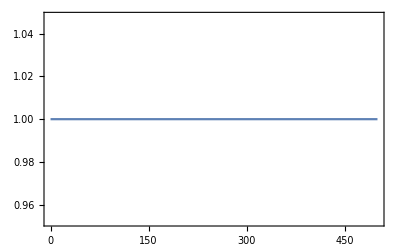

```mathematica
Plot[{Fav}/.{A->431},{Ω,0.0,500},Frame->True] (*54.30089595565897*)
```

```mathematica
(*Ok, that's working fine.*)
```

```mathematica
(*#################################################################################*)
(*#################################################################################*)
```

```mathematica
(*Next: take off-resonant drive into account and calculate fidelity of this process*)
```

```mathematica
M=4;
Ωo=Ω;
```

```mathematica
(*in this version, the free evolution with the phase Aτ is taken into account and corrected*)
V0table=Table[U2V0[2*τ,i,0,i-1,π],{i,M,4,-2}]/.{τ->π/(2*M*Ω)};
PrependTo[V0table,U0f[τ,M+1, π]/.{τ->π/(2*M*Ω)} //FullSimplify];
AppendTo[V0table,U1f[2*τ,2,0]/.{τ->π/(2*M*Ω)}];
AppendTo[V0table,U0f[τ,1,π]/.{τ->π/(2*M*Ω)} //FullSimplify];
V0table;
V0=Dot @@ V0table ;
V1table=Table[U2V1[2*τ,i,0,i-1,π],{i,M,4,-2}]/.{τ->π/(2*M*Ω)};
PrependTo[V1table,U1f[τ,M+1, π]/.{τ->π/(2*M*Ω)}];
AppendTo[V1table,U0f[2*τ,2,0]/.{τ->π/(2*M*Ω)} //FullSimplify];
AppendTo[V1table,U1f[τ,1,π]/.{τ->π/(2*M*Ω)}];
V1table;
V1=Dot @@ V1table ;
VOR=KroneckerProduct[{{1,0},{0,0}},V0]+KroneckerProduct[{{0,0},{0,1}},V1];
VcnotOR=Exp[-ⅈ*π/4]*KroneckerProduct[IdentityMatrix[2],MatrixExp[PauliMatrix[1]*ⅈ*π/4]].KroneckerProduct[MatrixExp[PauliMatrix[3]*ⅈ*π/4],IdentityMatrix[2]].VZ†.VOR;
Fav=(Abs[Tr[Ucnot.VcnotOR]]^2+4)/20/.{τ->π/(2*M*Ω)};
```

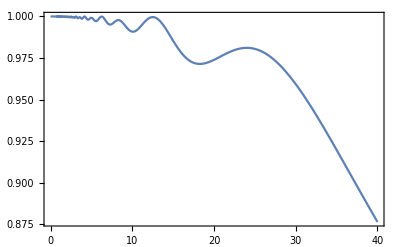

```mathematica
Plot[{Fav}/.{A->200},{Ω,0.0,40},Frame->True] (*The fidelity decreases with increasing driving strength, as expected. The synchronizable points are visible in the oscillatatory behaviour, but the fidelity is never fully recovered here, as the gate sequence assumes a free phase has to be corrected, but it does not as the off-resonant bloch vector has rotated around a different axis (one between z and x) and due to the off-resonant drive, it has at these points excatcly returned to its origial position and thus no evolution around the z-axis with Aτ has taken place. Thus, the attemt to correct the assumed rotation with the gate sequence leads to an error.*)
```

```mathematica
data1=Cases[Plot[{Fav}/.{A->200},{Ω,0.0,40},Frame->True],Line[data_]:>data,-4,1][[1]];
Export["fidelityA200.dat",data1,"Table"]
```

fidelityA200.dat

```mathematica
(*#################################################################################*)
(*#################################################################################*)
```

```mathematica
(*This is the version for the synchronized points. Here, the free evolution of the off-resonant transition returns to identity and therefore, not z-rotation does have to be corrected*)
```

```mathematica
(*Define synchronization condition for driving strength*)
f[A_,m_,M_,n_]:= A / Sqrt[((4*m*M)/n)^2-1]
```

```mathematica
(*Define variables*)
n=1;
m=1; 
M=4;
Ωo=Ω;
(*beachte: falls m gerade, muss am Schluss noch eine globale Phase von -1 korrigiert werden.*)
```

```mathematica
(*Values for driving strength at synchronized points, in units of kHz, a function of coupling A and repetition rate M of gate sequence*)
(*parallel hyperfine component in units of kHz, examples are: strongly coupled A=431 kHz, weakly coupled A=89kHz*)
N[Table[{f[A,m,M,n]/.A->431,M},{M,2,48,2}]]
```

{{26.9903,2.},{13.4753,4.},{8.98112,6.},{6.7352,8.},{5.38792,10.},{4.48983,12.},{3.84837,14.},{3.36729,16.},{2.99313,18.},{2.6938,20.},{2.4489,22.},{2.24482,24.},{2.07214,26.},{1.92413,28.},{1.79585,30.},{1.68361,32.},{1.58457,34.},{1.49654,36.},{1.41777,38.},{1.34688,40.},{1.28274,42.},{1.22444,44.},{1.1712,46.},{1.1224,48.}}

```mathematica
(*calculate time evolution operator with synchronized condition*)
```

```mathematica
V0table=Table[U2V0[2*τ,1,0,1,π],{i,M,4,-2}]/.{τ->π/(2*M*Ω)};
PrependTo[V0table,U0f[τ,1, π]/.{τ->π/(2*M*Ω)} //FullSimplify];
AppendTo[V0table,U1f[2*τ,1,0]/.{τ->π/(2*M*Ω)}];
AppendTo[V0table,U0f[τ,1,π]/.{τ->π/(2*M*Ω)} //FullSimplify];
V0table/.{A->431,Ω->13.475331358809568}
V1table=Table[U2V1[2*τ,1,0,1,π],{i,M,4,-2}]/.{τ->π/(2*M*Ω)};
PrependTo[V1table,U1f[τ,1, π]/.{τ->π/(2*M*Ω)}];
AppendTo[V1table,U0f[2*τ,1,0]/.{τ->π/(2*M*Ω)} //FullSimplify];
AppendTo[V1table,U1f[τ,1,π]/.{τ->π/(2*M*Ω)}];
V1table/.{A->431,Ω->13.475331358809568}
V0=Dot @@ V0table ;
V1=Dot @@ V1table ;
VOR=KroneckerProduct[{{1,0},{0,0}},V0]+KroneckerProduct[{{0,0},{0,1}},V1];
VcnotOR=Exp[-ⅈ*π/4]*KroneckerProduct[IdentityMatrix[2],MatrixExp[PauliMatrix[1]*ⅈ*π/4]].KroneckerProduct[MatrixExp[PauliMatrix[3]*ⅈ*π/4],IdentityMatrix[2]].VOR;
```

{{{1.+1.13255×10^-15 ⅈ,0.-3.54096×10^-17 ⅈ},{0.-3.54096×10^-17 ⅈ,1.-1.13255×10^-15 ⅈ}},{{0.92388+2.09269×10^-15 ⅈ,-8.6682×10^-16-0.382683 ⅈ},{8.6682×10^-16-0.382683 ⅈ,0.92388-2.09269×10^-15 ⅈ}},{{Cos[π/8],-ⅈ Sin[π/8]},{-ⅈ Sin[π/8],Cos[π/8]}},{{1.+1.13255×10^-15 ⅈ,0.-3.54096×10^-17 ⅈ},{0.-3.54096×10^-17 ⅈ,1.-1.13255×10^-15 ⅈ}}}

{{{Cos[π/16],ⅈ Sin[π/16]},{ⅈ Sin[π/16],Cos[π/16]}},{{0.92388+2.09269×10^-15 ⅈ,-8.6682×10^-16+0.382683 ⅈ},{8.6682×10^-16+0.382683 ⅈ,0.92388-2.09269×10^-15 ⅈ}},{{1.+2.26511×10^-15 ⅈ,0.+7.08192×10^-17 ⅈ},{0.+7.08192×10^-17 ⅈ,1.-2.26511×10^-15 ⅈ}},{{Cos[π/16],ⅈ Sin[π/16]},{ⅈ Sin[π/16],Cos[π/16]}}}

```mathematica
(*calculate fidelity, insert value for driving strength at synchronized points*)
```

```mathematica
Fav=(Abs[Tr[Ucnot.VcnotOR]]^2+4)/20/.{A->431,Ω->13.475331358809568}
(*parallel hyperfine component in units of kHz, examples are: strongly coupled A=431 kHz, weakly coupled A=89kHz*)
```

1.

```mathematica
ACHTUNG ich habe das m und n noch nicht in die Zeitevolutionsoperatoren geschrieben, und habe die Zeichen auch schon belegt...
```